```mathematica
(*  Constants defns *)
g = 9.81; (* accel grav *)
ρ = 1.17; (*Density of air *)
R = .00125; (* radius of seed, 2.5 mm diameter *)
d = .000324; (* thickness of seed, ~0.2mm avg thickness*)
m = .0000017;  (* mass of seed, ~2 mg *)
μ=.000018; (*dyn visc -- not in use*)
e=.5; (* induced drag efficiency -- for analytical drag*)

(* Coaster constants *)
(*g = 9.81; (* Acceleration due to gravity *)
ρ = 1.225; (* Density of air *)
R = .053; (* 5 cm radius coaster *)
d = .0017; (* Thickness ~ estimated. *)
m = .0059;  (* 5.9 g *)
ω = 49; (* Rotation rate in rad/s *)
μ=.000018; (*dynamic viscosity of air -- not currently used*)
e=.8; (* induced drag efficiency -- ellipitcal wing = 1, rectangular = 0.7 -- choose intermediate -- *)
L = 1/2 m*R^2*ω; (* ang mom. thin disc rotating about axis of symmetry *) *)
```

```mathematica
(* Make solver a function. This block sets up a function that solves the equation of motion for a flat, spinning disc in a way that enables repeated/looping calls to the function for batch simulation of a large number of runs with varied initial conditions. *)

(* Initial Conds & SOlver --- Need to redefine/recalculate forces INSIDE the functuon so that the vaired launch conditions are included in the force expressions *)
solveEquations[xo_,yo_,zo_,vxo_,vyo_,vzo_,αo_,ϕo_,ω_] := Module[{soln,disp,flighttime,zdisp},
Check[ (* Check is essentially a try-catch block, prevents a single error from stopping the entire remaining simulations *)
(* Force defns*)
V[t] = √(x'[t]^2+y'[t]^2+z'[t]^2); (* Velocity magnitude *)
L = 1/2 m*R^2*ω;(*Angular momentum magnitude *)
(* stall approximation sigmoid parameters *)
Subscript[α, crit] = 40*(2π/360);
Subscript[α, decay] = 0.1;
(* Angular momentum components in lab frame *)
Lx[t]=L*(x'[t]/V[t] Sin[α[t]]+y'[t]/V[t] Cos[α[t]]Cos[ϕ[t]]+z'[t]/V[t] Cos[α[t]]Sin[ϕ[t]]);
Ly[t]=L*(y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]);
Lz[t]=L*(z'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-x'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]);
(*Lift components in lab frame - defined using the above ang mom components*)
(* Lift as function of v and l components*)
FLx[t]=(((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])) (x'[t]^2+y'[t]^2+z'[t]^2) (Ly[t] x'[t] y'[t]+Lz[t] x'[t] z'[t]-Lx[t] (y'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2)))));
FLy[t]=-((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])) (x'[t]^2+y'[t]^2+z'[t]^2) (-y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t] (x'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2))));
FLz[t]=-((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay]))(Lz[t] (x'[t]^2+y'[t]^2)-(Lx[t] x'[t]+Ly[t] y'[t]) z'[t]) (x'[t]^2+y'[t]^2+z'[t]^2))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2))));



(* Drag force componenss. Using the experimentally determined value of CD for Ruellia seeds *)
(* Experimental drag expression based on measured Cd for R ciliatiflora *)
Subscript[C, D] = 0.7075; (* Calculated by conversion of the ballistic parameter k_d for all seeds with Re>= 2000 in FlightData spreadsheet. *)
Dx[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*x'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));
Dy[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*y'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));
Dz[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*z'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));


(* Experimental magnus exrpression based on measured Cm for R ciliatiflora *)
Subscript[C, M]=0.0351;(*5% uncertainity interval: (.018, .052) *)
Mx[t] =-1/2 Subscript[C, M] ρ(d*2R)V[t](y'[t](Sin[α[t]]*z'[t]/(√(x'[t]^2+z'[t]^2))-Cos[α[t]]Sin[ϕ[t]]*x'[t]/(√(x'[t]^2+z'[t]^2)))-z'[t](y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]));
My[t] = -1/2 Subscript[C, M] ρ(d*2R)V[t](z'[t](Sin[α[t]]*x'[t]/V[t]+Cos[α[t]]Cos[ϕ[t]]*y'[t]/V[t]+Cos[α[t]]Sin[ϕ[t]]*z'[t]/V[t])-x'[t](Sin[α[t]]*z'[t]/(√(x'[t]^2+z'[t]^2))-Cos[α[t]]Sin[ϕ[t]]*x'[t]/(√(x'[t]^2+z'[t]^2))));
Mz[t] =-1/2 Subscript[C, M] ρ(d*2R)V[t](x'[t](y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]])-y'[t](Sin[α[t]]*x'[t]/V[t]+Cos[α[t]]Cos[ϕ[t]]*y'[t]/V[t]+Cos[α[t]]Sin[ϕ[t]]*z'[t]/V[t]));
Subscript[eq, α] = α'[t] == (g *√(x'[t]^2+z'[t]^2))/V[t]^2 Cos[ϕ[t]]-(ρ*V[t]*π^2*R^2)/(2m)Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay]));
Subscript[eq, ϕ] = ϕ'[t] == -(π^3*R^3 ρ*V[t]^2)/(16*L)Sin[2*α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay]));
Subscript[eq, x] = x''[t]==1/m(FLx[t]+Dx[t]+Mx[t]);
Subscript[eq, y] = y''[t]== 1/m(FLy[t]+Dy[t]+My[t])-g;
Subscript[eq, z] = z''[t] ==1/m(FLz[t]+Dz[t]+Mz[t]);
soln = NDSolve[{

(* 5 ODES *)
 Subscript[eq, α],Subscript[eq, ϕ], Subscript[eq, x], Subscript[eq, y],Subscript[eq, z], 
(* Initial conditions *)
ϕ[0]==ϕo,
α[0]==αo,
x[0]==xo,x'[0]==vxo,
y[0]==yo,y'[0]==vyo,
z[0]==zo,z'[0]==vzo},

{α,ϕ,x,y,z},{t,0,12}]  ;

(* get time disc hits ground, total displacement and z displacement *)
flighttime = Part[FindRoot[0==y[t]/.soln,{t,.01,12}, Method->"Brent"],1] //Last;
disp=√(x[flighttime]^2+z[flighttime]^2)/.soln;
zdisp=z[flighttime]/.soln;
Return[{ϕo*(360/(2π)),αo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω,flighttime,Part[disp,1],Part[zdisp,1],soln}],
Print[{"Error:",ϕo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω}]; (* Error catching -- return the simulated conditions so you know where stuff is breaking *)
Return[{ϕo*(360/(2π)),αo*(360/(2π)),ArcTan[vyo/vxo]*(360/(2π)),ω,-1,-1,-1,-1}]]]
```

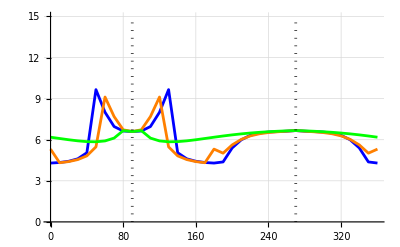

```mathematica
(* This block simulates dispersal range over all initial launch orientations at 3 different spin rates. It is used mainly as check that the simulation runs sufficiently quickly & can be used to make sure everything is working properly (errors will typically occur if something has broken) *)

(*Initial betas 95% interval (38,42) *)
(*Phi ~270 (backspin), but not really possible to measure precisely *)
(*Initial velocities 95% interval (9.00, 10.63)*)
angles = Range[0*((2*π)/360),360*((2*π)/360),10*((2*π)/360)];
Subscript[x, o]=0;
Subscript[y, o]=0.5;
Subscript[z, o]=0;
Subscript[α, o]=(.00001)*((2*π)/360);
Subscript[vx, o]=15*Cos[40*((2*π)/360)]; 
Subscript[vy, o]=15*Sin[40*((2*π)/360)];
Subscript[vz, o]=0; 



(* General form for running a set of simulations using the Table command. Passes in each element of the list "angles" to the solver, solves the equations using the above initial conditions and the given phi value. *)
resultsTable = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,1660*2π],{phi,angles}];
resultsTableMid = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,1000*2π],{phi,angles}];
resultsTableLow = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,200*2π],{phi,angles}];

(* For the vertical lines denoting top & backspin*)
topspin = Transpose@{{90,90},{0,15}};
backspin = Transpose@{{270,270},{0,15}};

(*Pull out the displacement data from the results table for each spin rate, plot against the launch orientation*)
datadisp = Transpose@{resultsTable[[All,1]],resultsTable[[All,6]]};
datadispMid = Transpose@{resultsTableMid[[All,1]],resultsTableMid[[All,6]]};
datadispLow = Transpose@{resultsTableLow[[All,1]],resultsTableLow[[All,6]]};

ListLinePlot[{datadisp,datadispMid,datadispLow, topspin,backspin},
PlotStyle->{{Blue},{Orange}, {Green},{Black,Dotted},{Black,Dotted}},
PlotRange->All, GridLines->Automatic]
```

{0,2.37259,5.31394,-2.00767}

{10,2.37902,4.31871,-0.12116}

{20,2.34588,4.40368,0.403948}

{30,2.34339,4.55,0.89834}

{40,2.37952,4.82135,1.35084}

{50,2.50428,5.47703,1.89304}

{60,2.67338,9.11735,2.76943}

{70,1.76685,7.69106,3.22076}

{80,1.41632,6.72535,1.38237}

{90,1.33725,6.59898,3.40777×10^-6}

{100,1.41632,6.72534,-1.38236}

{110,1.76684,7.69106,-3.22075}

{120,2.67337,9.11736,-2.76944}

{130,2.50428,5.47703,-1.89304}

{140,2.37952,4.82135,-1.35084}

{150,2.34339,4.55,-0.89834}

{160,2.34588,4.40368,-0.403949}

{170,2.37902,4.31872,0.12116}

{180,2.37259,5.31394,2.00767}

{190,2.08819,5.01843,2.85575}

{200,1.94656,5.62135,3.03886}

{210,1.81827,6.02267,2.92289}

{220,1.70339,6.27925,2.61865}

{230,1.60519,6.43398,2.19205}

{240,1.52665,6.52363,1.69068}

{250,1.46992,6.57862,1.14695}

{260,1.43632,6.62185,0.580185}

{270,1.42656,6.66802,-6.63585×10^-7}

{280,1.43632,6.62185,-0.580187}

{290,1.46992,6.57862,-1.14696}

{300,1.52665,6.52363,-1.69068}

{310,1.60519,6.43398,-2.19205}

{320,1.70339,6.27925,-2.61865}

{330,1.81827,6.02267,-2.92289}

{340,1.94656,5.62135,-3.03886}

{350,2.08819,5.01843,-2.85575}

{360,2.37259,5.31394,-2.00767}

-Graphics3D-

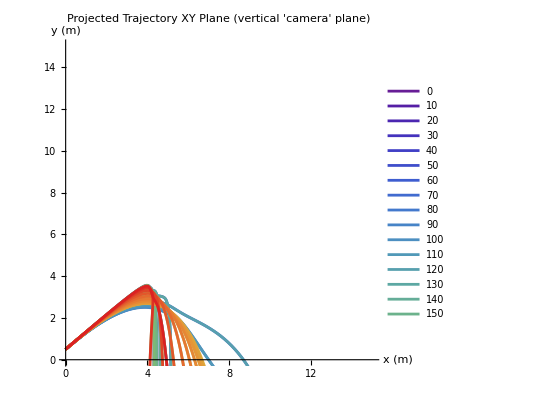

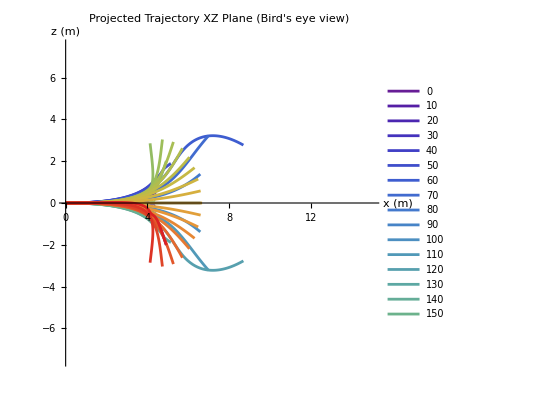

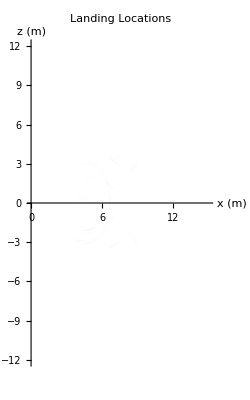

ColorData::notprop: {1,2,3,4,5,6,7,8,9,10,«27»} is not a known property for ColorData. Use ColorData["Properties"] for a list of properties.

Part::partw: Part 38 of … does not exist.

-Graphics-

```mathematica
(* This block simulates the flight of discs, but saves the entire 3d traectory & orientation data, not just the flight time and dispersal distance, so care should be taken to ensure that only a small number of simulations are run in this block, otherwise runtime will be quite long and the resulting data file will large. This is used to generate visualizations of the 3d trajectories of a flying disc. Additionally, this block also generates a scatter plot of the landing coordinates of the simulated discs colored by their launch orientation, which can be useful to demonstrate how various launch parameters influence the spread/dispersal shadow of launched discs.*)
plotListXYZ = {};
plotListXY = {};
plotListXZ = {};
plotListCoords = {};
resultsTablePhi = Table[solveEquations[0,0.5,0,Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[α, o],phi,1000*2π],{phi,angles}];
xcoords = {};
zcoords = {};
colorcoords = {};
dists = {};

(* Run simulation for each specified launch orientation phi *)
For[p=1, p<= Length[angles], p++,
Print[{resultsTablePhi[[p,1]],resultsTablePhi[[p,5]],resultsTablePhi[[p,6]],resultsTablePhi[[p,7]]}];
tland=resultsTablePhi[[p,5]];
soln=resultsTablePhi[[p,8]];
x[t]=soln{3};
y[t]=soln{4};
z[t]=soln{5};

(* save the landing coordinates of each simulation *)
xland = x[tland]/.soln;
zland = z[tland]/.soln;
AppendTo[dists,resultsTablePhi[[p,6]]];

AppendTo[xcoords,xland];
AppendTo[zcoords,zland];
AppendTo[colorcoords,p];

(* Plot the 3d trajectory of each simulated disc flight, as well as the projection of those trajectories in the XY (vertical) and XZ (floor) planes*)
plotXYZ = ParametricPlot3D[{x[t],y[t],z[t]}/.soln,{t,0,tland*1},
PlotRange->{{0,15},{0,5},{-7.5,7.5}}, 
PlotLabel->"3D trajectory ",
AxesLabel->{"x (m)","y (m)", "z (m)"},
PlotLegends->{resultsTablePhi[[p,1]]},
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
FaceGrids->{{1,0,0},{0,-1,0},{0,0,-1}},
ViewAngle->0.36449712460058503,ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,ViewPoint->{-1.205461023704569,3.136085324249023,0.40228417736599875},
ViewProjection->Automatic,
ViewRange->All,
ViewVector->Automatic,
ViewVertical->{0.12734601200290835,0.9914635570294913,-0.027982285635446663}];

plotXY = ParametricPlot[{{x[t],y[t]}/.soln},{t,0,tland*1.1},
PlotRange->{{0,15},{0,15}}, 
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
PlotLabel->"Projected Trajectory XY Plane (vertical 'camera' plane) ",
AxesLabel->{"x (m)", "y (m)"},
PlotLegends->{resultsTablePhi[[p,1]]}];

plotXZ = ParametricPlot[{{x[t],z[t]}/.soln},{t,0,tland},
PlotRange->{{0,15},{-7.5,7.5}}, 
PlotStyle->{ColorData["Rainbow",p/Length[angles]]},
PlotLabel->"Projected Trajectory XZ Plane (Bird's eye view)",
AxesLabel->{"x (m)", "z (m)"},
PlotLegends->{resultsTablePhi[[p,1]]}];

plotLandCoords = ParametricPlot[{{x[t],z[t]}/.soln},{t,tland,tland+0.001},
PlotRange->{{0,15},{-12,12}}, 
PlotStyle->{ColorData["Rainbow",p/Length[angles]], Thickness[0.02]},
PlotLabel->"Landing Locations",
AxesLabel->{"x (m)", "z (m)"}
(*,PlotLegends->{resultsTablePhi[[p,1]]}*)];


AppendTo[plotListXYZ,plotXYZ];
AppendTo[plotListXY,plotXY];
AppendTo[plotListXZ,plotXZ];
AppendTo[plotListCoords, plotLandCoords];


xsol = x/. First[soln];
ysol = y/. First[soln];
zsol = z/. First[soln];
ϕsol = ϕ/. First[soln];
αsol = α/. First[soln];
trajData = {};

(* Save trajectory data using the Export[] function if desired*)
temp = Table[{t,xsol[t], ysol[t], zsol[t], ϕsol[t], αsol[t]},{t,0,10,.01}];

Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\SeedTrajectoryPhi_"<>ToString[N[angles[[p]]*(360/(2π))]]<>"csv",temp
];
]
(* Show the generated plots in Mathematica and export them as jpgs *)
XYZ=Show[plotListXYZ]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXYZ.jpg",XYZ];
XY=Show[plotListXY]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXY.jpg",XY];
XZ=Show[plotListXZ]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combinedXZ.jpg",XZ];
coords = Show[plotListCoords]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\seed\\sd_combined_landing" <> ToString[omega1]<>".jpg",coords];

plotLandCoords = ListPlot[{xcoords,zcoords},
PlotRange->{{0,15},{-7.5,7.5}}, 
PlotStyle->{ColorData["Rainbow",colorcoords]},
PlotLabel->"Landing Coords",
AxesLabel->{"x (m)", "z (m)"},
PlotLegends->{resultsTablePhi[[p,1]]}
]
```

```mathematica
(* Simulate disc flights varying both launch angle and launch orientation and 3 distinct spin rates to generate contours of dispersal range as a function of these 3 parameters. (Figure 6 in "Backspin in Ruellia .... conditions")*)
angles = Range[80*((2*π)/360),460*((2*π)/360),2*((2*π)/360)]; (* Launch orientation angles for phi ϕ -- Symmetric about 270, so can cut this range to (90,270) if desired *)
anglesBeta = Range[0*((2*π)/360),65*((2*π)/360),2.5*((2*π)/360)]; (* angle between initial velocity and horizontal plane "elevation angle" *)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=500*2π;
L = .5*m*R^2*ω;
resultsTableBeta = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,ω],{phi,angles}, {beta,anglesBeta}];
resultsTableBeta2 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,1000*2π],{phi,angles}, {beta,anglesBeta}];
resultsTableBeta3 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],phi,1500*2π],{phi,angles}, {beta,anglesBeta}];
```

```mathematica
(* Contour plot the results of the above phi-beta-omegaa sim block *)
dispList = {};
dispList2={};
dispList3={};
zdispList = {};
zdispList2={};
zdispList3={};
For[p=1, p<= Length[angles], p++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta[[p,b,6]]}];
AppendTo[dispList2,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta2[[p,b,6]]}];
AppendTo[dispList3,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta3[[p,b,6]]}];
AppendTo[zdispList,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta[[p,b,7]]}];
AppendTo[zdispList2,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta2[[p,b,7]]}];
AppendTo[zdispList3,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),resultsTableBeta3[[p,b,7]]}];

]
]
(*Print[dispList]*)
contour = ListContourPlot[dispList,InterpolationOrder->1,Contours->Range[4,12,1], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dotted],
PlotLabel->"Dispersion range vs initial angles"];

contour2 = ListContourPlot[dispList2,InterpolationOrder->4,Contours->Range[6,12,1], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dotted],
PlotLabel->"Dispersion range vs initial angles"];

contour3 = ListContourPlot[dispList3,InterpolationOrder->1,Contours->10, 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{250,290},{25,55}},
GridLinesStyle->Directive[Black,Thick,Dashed],
PlotLabel->"Dispersion range vs initial angles"];

Show[contour]
Show[contour2]
Show[contour3]

(* contours of off-horizontal (z) displacement as a function of the angles *)
(*(*Print[dispList]*)
zcontour = ListContourPlot[zdispList,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];

zcontour2 = ListContourPlot[zdispList2,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];

zcontour3 = ListContourPlot[zdispList3,InterpolationOrder->1,Contours->Range[0,5,.5], 
ContourLabels->True,
PlotLegends->Automatic,
FrameLabel->{"ϕ_o","β_o"},
GridLines-> {{265,275},{38,42}},
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Off-horiz range vs initial angles"];
Show[zcontour]
Show[zcontour2]
Show[zcontour3]*)
```

```mathematica
(* Generate contours of dispersal range as a function of launch orientation and spin rate for 3 distinct launch angles. These plots are less dynamic than the previous batch, but still interesting. *)
angles = Range[80*((2*π)/360),460*((2*π)/360),2*((2*π)/360)]; (* Launch angles for phi ϕ -- Symmetric about 270, so can cut this range to (90,270) if desired *)
initialOmegas = 2π*Range[200,4000,100];
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[v, o]=10;
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
ω=1600;
resultsTableOmega = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[30*((2π)/360)],Subscript[v, o]*Sin[30*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
resultsTableOmega2 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[40*((2π)/360)],Subscript[v, o]*Sin[40*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
resultsTableOmega3 = Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[v, o]*Cos[50*((2π)/360)],Subscript[v, o]*Sin[50*((2π)/360)],Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles}, {omega,initialOmegas}];
```

```mathematica
(* Contour plot the results of the preceding simulation block*)
dispList = {};
dispList2 = {};
dispList3 = {};
zdispList = {};
For[p=1, p<= Length[angles], p++,
For[o=1,o<=Length[initialOmegas],o++,
AppendTo[dispList,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega[[p,o,6]]}];
AppendTo[dispList2,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega2[[p,o,6]]}];
AppendTo[dispList3,{angles[[p]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTableOmega3[[p,o,6]]}];


]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]

ListContourPlot[dispList2,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]

ListContourPlot[dispList3,InterpolationOrder->1,Contours->Range[0,16,.5], 
ContourLabels->True,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->{"ϕ_o","ω"},
GridLines-> { {265,275},{1122,1382,{3200,Directive[Black,Dashed]}} },
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Dispersion range: ϕ vs ω"]
```

```mathematica
(* Generate contours of dispersal range as a function of launch angle and spin rate for backspin (phi=270). Ultimately, spin rate does very little to impact trajectory or range in the backspin case, so these plots are mostly uninteresting. *)

initialOmegas = 2π*Range[200,4000,100];
anglesBeta = Range[0*((2*π)/360),65*((2*π)/360),2.5*((2*π)/360)]; (* angle between initial velocity and horizontal plane "elevation angle" *)

Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[v, o]=9.81;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=270*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

```mathematica
(* Contour the results of the above simulation block *)
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]]/(2π),anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]]/(2π),anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
contour = ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Backspin"];

Show[contour]
```

```mathematica
(* Same as above but for a launch orientation 'near' the range maximizing orientation. contour plot of dispersal range for varied launch angles and spin rates. Precise choise of phi for this plot will change it significantly. *)
initialOmegas = 2π*Range[200,4000,100];
anglesBeta = Range[0*((2*π)/360),65*((2*π)/360),2.5*((2*π)/360)]; (* angle between initial velocity and horizontal plane "elevation angle" *)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=0.5;
Subscript[z, o]=0;
Subscript[α, o]=(0)*((2*π)/360);
Subscript[ϕ, o]=140*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[40*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[40*((2π)/360)];
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a valid string pattern.

Clear::ssym: y_o is not a symbol or a valid string pattern.

Clear::ssym: z_o is not a symbol or a valid string pattern.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

```mathematica
(* Contour the results of the preceding simulation block *)
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]]/(2*π),anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]]/(2*π),anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Topspin"]
```

```mathematica
(* Same as above but for a launch orientation at sidespin, akin to a "forehand" or "wrist-flick" throw of a frisbee. contour plot of dispersal range for varied launch angles and spin rates. Precise choice of phi for this plot will change it significantly. *)
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360);
Subscript[ϕ, o]=180*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[45*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[45*((2π)/360)];
Subscript[vz, o]=0; 
Subscript[v, o]=10;
ω=1600;
resultsTableBetaOmega= Table[solveEquations[Subscript[x, o],Subscript[y, o],Subscript[z, o],Cos[beta]*Subscript[v, o],Sin[beta]*Subscript[v, o],Subscript[vz, o],Subscript[α, o],Subscript[ϕ, o],omega],{omega,initialOmegas}, {beta,anglesBeta}];
```

Clear::ssym: x_o is not a symbol or a string.

Clear::ssym: y_o is not a symbol or a string.

Clear::ssym: z_o is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

```mathematica
(* Contour the results of the preceding simulation block *)
dispList = {};
zdispList = {};
For[o=1, o<= Length[initialOmegas], o++,
For[b=1,b<=Length[anglesBeta],b++,
AppendTo[dispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,6]]}];
AppendTo[zdispList,{initialOmegas[[o]],anglesBeta[[b]]*(360/(2π)),resultsTableBetaOmega[[o,b,7]]}];

]
]
(*Print[dispList]*)
ListContourPlot[dispList,InterpolationOrder->1,Contours->20, 
ContourLabels->Automatic,
PlotLegends->Automatic,
FrameLabel->{"ω","β_o"},
PlotLabel->"Dispersion range: ω vs β_o - Sidespin"]
```

```mathematica
(* Full series of simulations. Simulate every combination of all parameters (launch orientation, launch angle, spin rate, launch height, launch velocity). This block sets up the lists of phi beta and omega, the next block executes the simulations. This will take a minimum of several hours to execute since the total number of simulations is ~500,000. Ranges and step sizes/resolutions of each parameter can be modified to shorten runtime as necessary. *)
phiLow=90;
phiHi=270;
betaLow=0;
betaHi=65;
omegaLow=100;
omegaHi=4000;
angles = Range[phiLow*((2*π)/360),phiHi*((2*π)/360),2*((2*π)/360)];
anglesBeta = Range[betaLow*((2*π)/360),betaHi*((2*π)/360),5*((2*π)/360)];
initialOmegas = Range[omegaLow*2π, omegaHi*2π,100*2π];
```

```mathematica
(* Execute simulation where all parameters are varied simultaneously. Monitors provide an overview of current progress into the simulation, expect the full batch of simulations to take a minimum of 3 hours to complete if parameter ranges and resolutions are not changed. Note that a small number of simulations (on the order of 50/500000) will fail to execute (typically when beta is very high and spin rate is very low) because the root finder fails to find the seed's landing point. When this occurs, -1 will be stored for the time of flight, dispersal distance etc. *)
$HistoryLength=10;
Clear[Subscript[x, o],Subscript[y, o],Subscript[z, o],Subscript[α, o],Subscript[ϕ, o],Subscript[vx, o],Subscript[vy, o],Subscript[vz, o],Subscript[v, o],ω]
Subscript[x, o]=0;
Subscript[y, o]=1;
Subscript[z, o]=0;
Subscript[v, o] = 10;
Subscript[α, o]=(0.00001)*((2*π)/360);
Subscript[ϕ, o]=180*((2*π)/360);
Subscript[vx, o] = Subscript[v, o]*Cos[45*((2π)/360)];
Subscript[vy, o] = Subscript[v, o]*Sin[45*((2π)/360)];
Subscript[vz, o]=0; 
ω=1600;
Monitor[
resultsTablePhiBetaOmega75h15v= Table[solveEquations[Subscript[x, o],0.75,Subscript[z, o],Cos[beta]*15,Sin[beta]*15,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 1"]

Monitor[
resultsTablePhiBetaOmega75h10v= Table[solveEquations[Subscript[x, o],.75,Subscript[z, o],Cos[beta]*10,Sin[beta]*10,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 2"]
Monitor[
resultsTablePhiBetaOmega75h5v= Table[solveEquations[Subscript[x, o],.75,Subscript[z, o],Cos[beta]*5,Sin[beta]*5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 3"]

Monitor[
resultsTablePhiBetaOmega5h15v= Table[solveEquations[Subscript[x, o],.5,Subscript[z, o],Cos[beta]*15,Sin[beta]*15,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 4"]

Monitor[
resultsTablePhiBetaOmega5h10v= Table[solveEquations[Subscript[x, o],.5,Subscript[z, o],Cos[beta]*10,Sin[beta]*10,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 5"]
Monitor[
resultsTablePhiBetaOmega5h5v= Table[solveEquations[Subscript[x, o],.5,Subscript[z, o],Cos[beta]*5,Sin[beta]*5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 6"]

Monitor[
resultsTablePhiBetaOmega25h15v= Table[solveEquations[Subscript[x, o],.25,Subscript[z, o],Cos[beta]*15,Sin[beta]*15,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 7"]

Monitor[
resultsTablePhiBetaOmega25h10v= Table[solveEquations[Subscript[x, o],.25,Subscript[z, o],Cos[beta]*10,Sin[beta]*10,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 8"]
Monitor[
resultsTablePhiBetaOmega25h5v= Table[solveEquations[Subscript[x, o],.25,Subscript[z, o],Cos[beta]*5,Sin[beta]*5,Subscript[vz, o],Subscript[α, o],phi,omega],{phi,angles},{omega,initialOmegas}, {beta,anglesBeta}],
Grid[
{{Text[Style["Phi :",Darker[Blue,0.66]]],ProgressIndicator[phi,{phiLow*((2π)/360),phiHi*((2π)/360)}],Text[Style["ϕ: ",Darker[Blue,0.66]]],phi*(360/(2π))},
{Text[Style["Omega :",Darker[Blue,0.66]]],ProgressIndicator[omega,{omegaLow*2π,omegaHi*2π}],Text[Style["ω: ",Darker[Blue,0.66]]],omega*(1/(2π))},
{Text[Style["Beta :",Darker[Blue,0.66]]],ProgressIndicator[beta,{betaLow*((2π)/360),betaHi*((2π)/360)}],Text[Style["β: ",Darker[Blue,0.66]]],beta*(360/(2π))}
},Alignment->Left,Dividers->Center]];
Print["Completed simset 9"]



(* Process and aggregate data into useful form *)
aggregatedData = {};
For[b=1,b<=Length[anglesBeta],b++,
Print[b];
For[o=1, o<= Length[initialOmegas], o++,
For[p=1,p<=Length[angles],p++,
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 15, resultsTablePhiBetaOmega75h15v[[p,o,b,5]],resultsTablePhiBetaOmega75h15v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 10, resultsTablePhiBetaOmega75h10v[[p,o,b,5]],resultsTablePhiBetaOmega75h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 5, resultsTablePhiBetaOmega75h5v[[p,o,b,5]],resultsTablePhiBetaOmega75h5v[[p,o,b,6]]}];

AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 15, resultsTablePhiBetaOmega5h15v[[p,o,b,5]],resultsTablePhiBetaOmega5h15v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 10, resultsTablePhiBetaOmega5h10v[[p,o,b,5]],resultsTablePhiBetaOmega5h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 5, resultsTablePhiBetaOmega5h5v[[p,o,b,5]],resultsTablePhiBetaOmega5h5v[[p,o,b,6]]}];

AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 15, resultsTablePhiBetaOmega25h15v[[p,o,b,5]],resultsTablePhiBetaOmega25h15v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 10, resultsTablePhiBetaOmega25h10v[[p,o,b,5]],resultsTablePhiBetaOmega25h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 5, resultsTablePhiBetaOmega25h5v[[p,o,b,5]],resultsTablePhiBetaOmega25h5v[[p,o,b,6]]}];
]
]
]
aggregatedData
```

Clear::ssym: x_o is not a symbol or a valid string pattern.

Clear::ssym: y_o is not a symbol or a valid string pattern.

Clear::ssym: z_o is not a symbol or a valid string pattern.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at t == 3.56264; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.21456} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,0,5000 π}

NDSolve::ndcf: Repeated convergence test failure at t == 10.0837; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,90,65,7800 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.235915,ComplexInfinity,-2.59708,ComplexInfinity,-0.221733,ComplexInfinity,6.60797,8.47744} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.42214,3.17318,-0.235915,-2.27619,-2.59708,-0.190535,-0.221733,-0.709389,4.99584}.

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.235915,ComplexInfinity,-2.59708,ComplexInfinity,-0.221733,ComplexInfinity,6.60797,8.47744} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.42214,3.17318,-0.235915,-2.27619,-2.59708,-0.190535,-0.221733,-0.709389,4.99584}.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.235915,ComplexInfinity,-2.59708,ComplexInfinity,-0.221733,ComplexInfinity,6.60797,8.47744} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.42214,3.17318,-0.235915,-2.27619,-2.59708,-0.190535,-0.221733,-0.709389,4.99584}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.42214, step size is effectively zero; singularity or stiff system suspected.

{Error:,126,60,400 π}

NDSolve::ndsz: At t == 9.54639, step size is effectively zero; singularity or stiff system suspected.

{Error:,126,50,600 π}

NDSolve::ndsz: At t == 2.62225, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,162,60,600 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,176,60,800 π}

Completed simset 1

NDSolve::ndcf: Repeated convergence test failure at t == 5.34493; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.05939} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,60,4600 π}

NDSolve::ndcf: Repeated convergence test failure at t == 3.47813; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,90,45,5200 π}

NDSolve::ndcf: Repeated convergence test failure at t == 7.29309; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

{Error:,90,5,6000 π}

{Error:,90,55,6800 π}

{Error:,90,10,7000 π}

{Error:,90,25,7000 π}

{Error:,90,20,7400 π}

{Error:,90,45,8000 π}

{Error:,90,60,8000 π}

NDSolve::ndsz: At t == 8.54548, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,110,55,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.161024,ComplexInfinity,-2.81426,ComplexInfinity,-0.13063,ComplexInfinity,3.12069,4.33336} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {6.89549,2.72312,-0.161024,-13.9652,-2.81426,-0.174446,-0.13063,-0.833036,4.90717}.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,124,55,400 π}

NDSolve::ndsz: At t == 4.45595, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,148,60,400 π}

NDSolve::ndsz: At t == 3.64, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{Error:,162,55,600 π}

{Error:,164,65,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.112603,ComplexInfinity,-2.25059,ComplexInfinity,-0.159915,ComplexInfinity,8.84772,6.61779} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {4.81287,1.8291,-0.112603,-7.9128,-2.25059,0.515752,-0.159915,-0.536412,4.87117}.

{Error:,184,65,600 π}

Completed simset 2

NDSolve::ndcf: Repeated convergence test failure at t == 4.28886; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.0218} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,20,3600 π}

NDSolve::ndcf: Repeated convergence test failure at t == 6.38352; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,90,0,4800 π}

NDSolve::ndcf: Repeated convergence test failure at t == 5.94466; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

{Error:,90,65,5200 π}

{Error:,90,10,5400 π}

{Error:,90,(180 ArcTan[(-1+√3)/(1+√3)])/π,5600 π}

{Error:,90,20,5600 π}

{Error:,90,50,6000 π}

{Error:,90,(180 ArcTan[(-1+√3)/(1+√3)])/π,6200 π}

{Error:,90,65,6200 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,90,35,6600 π}

{Error:,90,(180 ArcTan[(-1+√3)/(1+√3)])/π,6800 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,90,25,6800 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,90,30,7000 π}

{Error:,90,45,7200 π}

{Error:,90,50,7200 π}

{Error:,90,65,7200 π}

{Error:,90,30,7400 π}

{Error:,90,5,7800 π}

{Error:,90,60,7800 π}

{Error:,90,20,8000 π}

{Error:,90,55,8000 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.121705,ComplexInfinity,-2.16671,ComplexInfinity,-0.187824,ComplexInfinity,8.59392,6.18006} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {6.0465,2.04603,-0.121705,-13.73,-2.16671,0.248308,-0.187824,-0.480888,4.89131}.

{Error:,152,35,600 π}

NDSolve::mxst: Maximum number of 2074096 steps reached at the point t == 7.67066.

{Error:,162,50,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.117716,ComplexInfinity,-2.19979,ComplexInfinity,-0.175366,ComplexInfinity,8.7456,6.38941} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {5.88937,1.80804,-0.117716,-13.3166,-2.19979,0.380293,-0.175366,-0.504674,4.88247}.

{Error:,164,40,600 π}

NDSolve::ndsz: At t == 1.74309, step size is effectively zero; singularity or stiff system suspected.

{Error:,194,65,400 π}

NDSolve::ndsz: At t == 9.56218, step size is effectively zero; singularity or stiff system suspected.

{Error:,196,60,600 π}

NDSolve::ndsz: At t == 6.4765, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{Error:,204,65,600 π}

Completed simset 3

NDSolve::ndcf: Repeated convergence test failure at t == 9.56122; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,5,5400 π}

NDSolve::ndcf: Repeated convergence test failure at t == 9.61913; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,(180 ArcTan[(-1+√3)/(1+√3)])/π,6600 π}

NDSolve::ndcf: Repeated convergence test failure at t == 8.87241; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,90,50,6800 π}

NDSolve::ndsz: At t == 3.42215, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,126,60,400 π}

NDSolve::ndsz: At t == 9.5464, step size is effectively zero; singularity or stiff system suspected.

{Error:,126,50,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.162435,ComplexInfinity,-2.06024,ComplexInfinity,-0.323923,ComplexInfinity,6.27135,4.22668} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {2.62224,2.91373,-0.162435,-0.150588,-2.06024,0.308294,-0.323923,-0.2946,4.97356}.

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.162435,ComplexInfinity,-2.06024,ComplexInfinity,-0.323923,ComplexInfinity,6.27135,4.22668} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {2.62224,2.91373,-0.162435,-0.150588,-2.06024,0.308294,-0.323923,-0.2946,4.97356}.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,162,60,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.0862369,ComplexInfinity,-2.16059,ComplexInfinity,-0.267676,ComplexInfinity,4.23581,2.25341} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {8.35739,3.01677,-0.0862369,-16.5693,-2.16059,0.529877,-0.267676,-0.184074,4.88334}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,176,60,800 π}

Completed simset 4

NDSolve::ndcf: Repeated convergence test failure at t == 6.73851; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,35,4800 π}

NDSolve::ndcf: Repeated convergence test failure at t == 10.1093; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,50,5000 π}

NDSolve::ndcf: Repeated convergence test failure at t == 5.6059; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,90,65,6400 π}

{Error:,90,20,7600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.225721,ComplexInfinity,-2.8928,ComplexInfinity,0.168866,ComplexInfinity,0.741419,1.09406} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {8.43518,3.0562,0.225721,-18.5659,-2.8928,-0.395392,0.168866,-0.986362,4.67752}.

{Error:,110,55,400 π}

NDSolve::mxst: Maximum number of 3554091 steps reached at the point t == 6.86033.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,124,55,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.195399,ComplexInfinity,-2.73447,ComplexInfinity,-0.169753,ComplexInfinity,4.56745,6.16573} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {4.45593,2.16155,-0.195399,-7.19418,-2.73447,0.164117,-0.169753,-0.779063,4.94588}.

{Error:,148,60,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.129564,ComplexInfinity,-2.11756,ComplexInfinity,-0.213063,ComplexInfinity,8.19017,5.74649} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.63999,2.43488,-0.129564,-4.87004,-2.11756,0.366144,-0.213063,-0.437193,4.90847}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,162,55,600 π}

NDSolve::ndsz: At t == 7.41733, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,164,65,400 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,184,65,600 π}

Completed simset 5

NDSolve::ndcf: Repeated convergence test failure at t == 9.7857; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,65,2200 π}

NDSolve::ndcf: Repeated convergence test failure at t == 4.99922; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.03774} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,90,20,2800 π}

NDSolve::ndcf: Repeated convergence test failure at t == 5.53463; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

{Error:,90,35,4200 π}

{Error:,90,25,4600 π}

{Error:,90,35,4600 π}

{Error:,90,55,4600 π}

{Error:,90,10,4800 π}

{Error:,90,40,4800 π}

{Error:,90,50,5000 π}

{Error:,90,30,5400 π}

{Error:,90,30,5600 π}

{Error:,90,45,6000 π}

{Error:,90,5,6400 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,90,45,6800 π}

{Error:,90,5,7000 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,90,10,7000 π}

{Error:,90,5,7200 π}

{Error:,90,35,7400 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,90,50,7400 π}

{Error:,90,40,8000 π}

{Error:,90,45,8000 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.121705,ComplexInfinity,-2.16671,ComplexInfinity,-0.187824,ComplexInfinity,8.59392,6.18006} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {6.0465,2.04603,-0.121705,-13.98,-2.16671,0.248308,-0.187824,-0.480888,4.89131}.

{Error:,152,35,600 π}

NDSolve::ndsz: At t == 7.70716, step size is effectively zero; singularity or stiff system suspected.

{Error:,162,50,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.117716,ComplexInfinity,-2.19979,ComplexInfinity,-0.175366,ComplexInfinity,8.7456,6.38941} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {5.88937,1.80804,-0.117716,-13.5666,-2.19979,0.380293,-0.175366,-0.504674,4.88247}.

{Error:,164,40,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.391197,ComplexInfinity,-2.04603,ComplexInfinity,-0.451706,ComplexInfinity,8.57755,8.47046} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {1.74306,0.913614,-0.391197,-1.67519,-2.04603,0.371429,-0.451706,-0.421722,5.22222}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,194,65,400 π}

{Error:,196,60,600 π}

{Error:,204,65,600 π}

Completed simset 6

NDSolve::ndcf: Repeated convergence test failure at t == 3.5977; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.00575} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,10,7000 π}

NDSolve::ndcf: Repeated convergence test failure at t == 4.6798; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,90,30,7200 π}

NDSolve::ndcf: Repeated convergence test failure at t == 7.42437; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

{Error:,90,30,7800 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.235915,ComplexInfinity,-2.59708,ComplexInfinity,-0.221733,ComplexInfinity,6.60796,8.47743} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.42214,3.17318,-0.235915,-2.77618,-2.59708,-0.190535,-0.221733,-0.709389,4.99584}.

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.235915,ComplexInfinity,-2.59708,ComplexInfinity,-0.221733,ComplexInfinity,6.60796,8.47743} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {3.42214,3.17318,-0.235915,-2.77618,-2.59708,-0.190535,-0.221733,-0.709389,4.99584}.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,126,60,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.101722,ComplexInfinity,-2.38639,ComplexInfinity,-0.129563,ComplexInfinity,8.52695,6.76855} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {9.5464,4.30321,-0.101722,-20.5141,-2.38639,-0.343109,-0.129563,-0.606738,4.84807}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,126,50,600 π}

NDSolve::ndsz: At t == 2.62225, step size is effectively zero; singularity or stiff system suspected.

{Error:,162,60,600 π}

{Error:,176,60,800 π}

Completed simset 7

NDSolve::ndcf: Repeated convergence test failure at t == 7.23907; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,5,2800 π}

NDSolve::ndcf: Repeated convergence test failure at t == 4.24133; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.00517} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,90,25,3000 π}

NDSolve::ndcf: Repeated convergence test failure at t == 5.35557; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

{Error:,90,65,4400 π}

{Error:,90,5,5200 π}

{Error:,90,35,5600 π}

{Error:,90,55,7000 π}

{Error:,90,30,7600 π}

{Error:,90,30,7800 π}

{Error:,90,20,8000 π}

{Error:,90,65,8000 π}

NDSolve::ndsz: At t == 8.54544, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,110,55,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.161024,ComplexInfinity,-2.81426,ComplexInfinity,-0.13063,ComplexInfinity,3.12068,4.33334} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {6.89549,2.72312,-0.161024,-14.4652,-2.81426,-0.174446,-0.13063,-0.833037,4.90717}.

{Error:,124,55,400 π}

NDSolve::ndsz: At t == 4.45594, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,148,60,400 π}

NDSolve::ndsz: At t == 3.64, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,162,55,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {0.202477,ComplexInfinity,-2.89736,ComplexInfinity,0.142264,ComplexInfinity,0.598715,0.882544} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {7.29475,1.82633,0.202477,-15.5103,-2.89736,0.304484,0.142264,-1.00708,4.68354}.

{Error:,164,65,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.112603,ComplexInfinity,-2.25059,ComplexInfinity,-0.159915,ComplexInfinity,8.84772,6.61779} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {4.81287,1.8291,-0.112603,-8.4128,-2.25059,0.515752,-0.159915,-0.536413,4.87117}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

{Error:,184,65,600 π}

Completed simset 8

NDSolve::ndcf: Repeated convergence test failure at t == 7.87823; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,65,2600 π}

NDSolve::ndcf: Repeated convergence test failure at t == 10.9327; unable to continue.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{Error:,90,65,3000 π}

NDSolve::ndcf: Repeated convergence test failure at t == 7.28567; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Error:,90,(180 ArcTan[(-1+√3)/(1+√3)])/π,4000 π}

{Error:,90,0,4400 π}

{Error:,90,45,4800 π}

{Error:,90,20,5000 π}

{Error:,90,55,5000 π}

{Error:,90,5,5400 π}

{Error:,90,0,5600 π}

{Error:,90,50,5600 π}

{Error:,90,50,5800 π}

{Error:,90,50,6000 π}

{Error:,90,30,6200 π}

{Error:,90,45,6600 π}

{Error:,90,25,7000 π}

{Error:,90,30,7200 π}

{Error:,90,65,7200 π}

{Error:,90,0,7400 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,90,5,7400 π}

{Error:,90,10,7600 π}

{Error:,90,(180 ArcTan[(-1+√3)/(1+√3)])/π,7600 π}

{Error:,90,45,7600 π}

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

{Error:,90,5,7800 π}

{Error:,90,50,7800 π}

NDSolve::ndsz: At t == 6.04649, step size is effectively zero; singularity or stiff system suspected.

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

General::stop: Further output of FindRoot::bbrac will be suppressed during this calculation.

{Error:,152,35,600 π}

NDSolve::ndsz: At t == 7.70716, step size is effectively zero; singularity or stiff system suspected.

{Error:,162,50,400 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.117716,ComplexInfinity,-2.19979,ComplexInfinity,-0.175366,ComplexInfinity,8.7456,6.3894} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {5.88937,1.80804,-0.117716,-13.8166,-2.19979,0.380293,-0.175366,-0.504673,4.88247}.

NDSolve::ndsz: At t == 5.88937, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{Error:,164,40,600 π}

Power::infy: Infinite expression 1/(√0.) encountered.

NDSolve::nlnum: The function value {-0.391198,ComplexInfinity,-2.04603,ComplexInfinity,-0.451708,ComplexInfinity,8.57753,8.47042} is not a list of numbers with dimensions {8} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],α[t],ϕ[t]} = {1.74306,0.913614,-0.391198,-1.92519,-2.04603,0.371429,-0.451708,-0.42172,5.22222}.

{Error:,194,65,400 π}

{Error:,196,60,600 π}

{Error:,204,65,600 π}

Completed simset 9

1

Part::partd: Part specification resultsTablePhiBetaOmega75h75v⟦1,1,1,5⟧ is longer than depth of object.

Part::partd: Part specification resultsTablePhiBetaOmega75h75v⟦1,1,1,6⟧ is longer than depth of object.

Part::partd: Part specification resultsTablePhiBetaOmega5h75v⟦1,1,1,5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

2

3

4

5

6

7

8

9

10

11

12

13

14

```mathematica
aggregatedData = {};
For[b=1,b<=Length[anglesBeta],b++,
Print[b];
For[o=1, o<= Length[initialOmegas], o++,
For[p=1,p<=Length[angles],p++,
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 15, resultsTablePhiBetaOmega75h15v[[p,o,b,5]],resultsTablePhiBetaOmega75h15v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 10, resultsTablePhiBetaOmega75h10v[[p,o,b,5]],resultsTablePhiBetaOmega75h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.75, 5, resultsTablePhiBetaOmega75h5v[[p,o,b,5]],resultsTablePhiBetaOmega75h5v[[p,o,b,6]]}];

AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 15, resultsTablePhiBetaOmega5h15v[[p,o,b,5]],resultsTablePhiBetaOmega5h15v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 10, resultsTablePhiBetaOmega5h10v[[p,o,b,5]],resultsTablePhiBetaOmega5h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.5, 5, resultsTablePhiBetaOmega5h5v[[p,o,b,5]],resultsTablePhiBetaOmega5h5v[[p,o,b,6]]}];

AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 15, resultsTablePhiBetaOmega25h15v[[p,o,b,5]],resultsTablePhiBetaOmega25h15v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 10, resultsTablePhiBetaOmega25h10v[[p,o,b,5]],resultsTablePhiBetaOmega25h10v[[p,o,b,6]]}];
AppendTo[aggregatedData,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π), 0.25, 5, resultsTablePhiBetaOmega25h5v[[p,o,b,5]],resultsTablePhiBetaOmega25h5v[[p,o,b,6]]}];
]
]
]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

```mathematica
b
o
p
```

13

33

77

```mathematica
Return
```

```mathematica
(* Save and/or export this big batch of data!*)
Save["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\sd_v2_2.csv",aggregatedData]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\sd_v2_2_2.csv", aggregatedData]
```

C:\Users\hesse\Desktop\F21\Thesis\SimData\sd_v2_2_2.csv

```mathematica
(* DEPRECATED: USE MATLAB PLOTTING SCRIPTS INSTEAD!!!!
Process data to generate contour of range maximizing orientation versus beta and omega.*)
(*1 - beta 
2 - omega
3 - phi 
4 - dep var (disp)*)

overallList1 = {};
overallList75 = {};
overallList5 = {};
dispList1 = {};
dispList5 = {};
dispList75 = {};
bestList1 = {};
bestList75 = {};
bestList5 = {};
worstList1 = {};
worstList75 = {};
worstList5 = {};
diffList1 = {};
diffList75 = {};
diffList5 = {};
For[b=1,b<=Length[anglesBeta],b++,
For[o=1, o<= Length[initialOmegas], o++,
maxrange1 = 0;
bestPhi1=0;
minrange1 = 1000;
worstPhi1=0;
maxrange75 = 0;
bestPhi75=0;
minrange75 = 1000;
worstPhi75=0;
maxrange5 = 0;
bestPhi5=0;
minrange5 = 1000;
worstPhi5=0;
For[p=1,p<=Length[angles],p++,

range1 = resultsTablePhiBetaOmega1[[p,o,b,6]];
If[range1>maxrange1,maxrange1=range1;bestPhi1=angles[[p]](360/(2π))];
If[range1<minrange1,minrange1=range1;worstPhi1=angles[[p]](360/(2π))];

range75 = resultsTablePhiBetaOmega75[[p,o,b,6]];
If[range75>maxrange75,maxrange75=range75;bestPhi75=angles[[p]](360/(2π))];
If[range1<minrange75,minrange75=range1;worstPhi75=angles[[p]](360/(2π))];

range5 = resultsTablePhiBetaOmega5[[p,o,b,6]];
If[range5>maxrange5,maxrange5=range5;bestPhi5=angles[[p]](360/(2π))];
If[range1<minrange5,minrange5=range1;worstPhi5=angles[[p]](360/(2π))];

AppendTo[dispList1,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega1[[p,o,b,1;;6]]}];
AppendTo[dispList75,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega75[[p,o,b,1;;6]]}];
AppendTo[dispList5,{angles[[p]]*(360/(2π)),anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),resultsTablePhiBetaOmega5[[p,o,b,1;;6]]}];

];
AppendTo[bestList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi1}];
AppendTo[bestList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi75}];
AppendTo[bestList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi5}];
AppendTo[worstList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi1}];
AppendTo[worstList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi75}];
AppendTo[worstList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),worstPhi5}];
AppendTo[diffList1,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi1-worstPhi1}];
AppendTo[diffList75,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi75-worstPhi75}];
AppendTo[diffList5,{anglesBeta[[b]]*(360/(2π)),initialOmegas[[o]]/(2π),bestPhi5-worstPhi5}];
];
];
dispList;
```

```mathematica
(*  saved calculation results*)
Save["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\bm_bestPhi_v2",{bestList1,bestList75,bestList5,worstList1,worstList75,worstList5,diffList1,diffList5,diffList75,dispList1,dispList75,dispList5}]
```

```mathematica
(* Load calculation results from file *)
Get["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\sd_bestPhi_v2"]
```

{{90.,0,200,{90.,0.1,0,400 π,0.318781,2.87951}},{92.5,0,200,{92.5,0.1,0,400 π,0.319325,2.88346}},{95.,0,200,{95.,0.1,0,400 π,0.321767,2.90308}},{97.5,0,200,{97.5,0.1,0,400 π,0.32621,2.9397}},93944,{265.,64,4000,{265.,0.1,64,8000 π,1.70019,5.29343}},{267.5,64,4000,{267.5,0.1,64,8000 π,1.69668,5.30503}},{270.,64,4000,{270.,0.1,64,8000 π,1.69581,5.31601}}}
 |  |  |  |

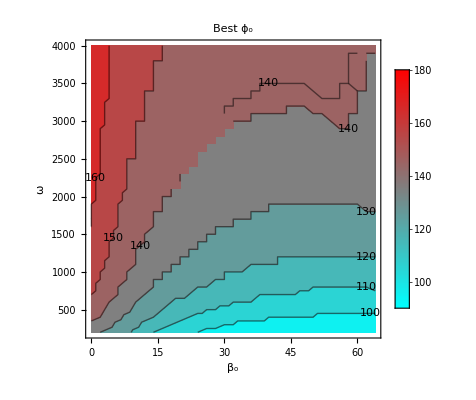

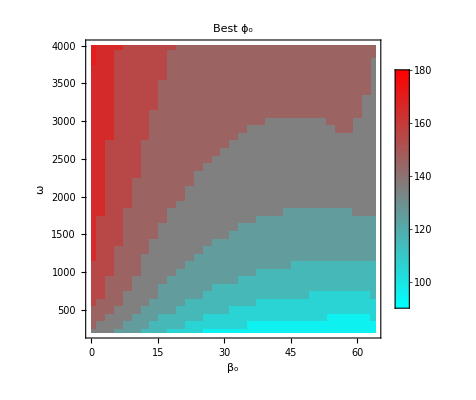

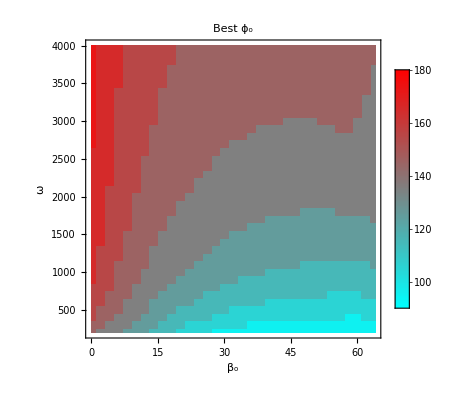

```mathematica
plotBP1=ListContourPlot[bestList1,InterpolationOrder->1, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP1.jpg",plotBP1];

plotBP75=ListContourPlot[bestList75,InterpolationOrder->0, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP75.jpg",plotBP75];

plotBP5=ListContourPlot[bestList5,InterpolationOrder->0, Contours->Range[90,180,10],
ColorFunction->(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{(Blend[{{90,Cyan},{0,White},{180,Red}},#]&),{90,180}}],
FrameLabel->{"β_o", "ω"},
ContourLabels->All,
GridLinesStyle->Directive[Black,Thick],
PlotLabel->"Best ϕ_o"]
Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\functional\\seed\\sd_TEMP5.jpg",plotBP5];
```

```mathematica
(*ListContourPlot3D[dispList,Contours->25,ColorFunction->"TemperatureMap",AxesLabel->{"ϕ","β","ω"},
ViewPoint->{0,0,Infinity}]*)
ListSliceContourPlot3D[dispList,
{"ZStackedPlanes",3},
AxesLabel->{"ϕ_o","β_o","ω"}]
```

-Graphics3D-